# The Hamiltonian in the Post-Minkowski Approximation

A notebook dedicated to calculating the equations necessary for the Post-Minkowski approximation of the Hamiltonian. This is another method of approximated general relativistic effects, though not as commonly used as the Post-Newtonian approximation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Basic definitions

This cell evaluates some of the basic definitions that are used in the equations. ndim represents the number of dimension, nbody the number of bodies in the simulation. position is a list containing the x, y, and z (depending on the number of dimensions) positions of each body. p is another vector, containing the x, y, and z components of momentum for each body. m is another list, which contains the masses of all three bodies.

```mathematica
ndim=2;
nbody=2;
If[ndim==2,
position={{qax,qay},{qbx,qby}};
p={{pax,pay},{pbx,pby}};
m={ma,mb};
xdot={{qaxdot1,qaydot1},{qbxdot1,qbydot1}};
pdot={{paxdot1,paydot1},{pbxdot1,pbydot1}};
,
position={{qax,qay,qaz},{qbx,qby,qbz}};
p={{pax,pay,paz},{pbx,pby,pbz}};
m={ma,mb};
xdot={{qaxdot1,qaydot1,qazdot1},{qbxdot1,qbydot1,qbzdot1}};
pdot={{paxdot1,paydot1,pazdot1},{pbxdot1,pbydot1,pbzdot1}};
]
If[nbody==3,
If[ndim==3,
AppendTo[position,{qcx,qcy,qcz}];
AppendTo[p,{pcx,pcy,pcz}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1,qczdot1}];
AppendTo[pdot,{pcxdot1,pcydot1,pczdot1}];
,
AppendTo[position,{qcx,qcy}];
AppendTo[p,{pcx,pcy}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1}];
AppendTo[pdot,{pcxdot1,pcydot1}];
]
]
```

## Functions

These functions listed are used for writing the PM approximation in Mathematica code. They allow for different vector operations. As well, two special functions, mline and y are defined, which correspond to two values in the PM approximation.

```mathematica
Normv[x_List] := Sqrt[x.x]
Normvector[x_List] := x/Normv[x]
rab[a_Integer,b_Integer] := position[[a]] - position[[b]]
Normvsq[x_List] := x.x
nhat[a_Integer,b_Integer] := Normvector[rab[a,b]]
nhatx[a_Integer,b_Integer,i_Integer] := nhat[a,b][[i]]
rdot[a_Integer,b_Integer] := xdot[[a]] - xdot[[b]]
R[a_Integer,b_Integer] :=Normv[rab[a,b]]
psq[a_Integer] := p[[a]].p[[a]]
mline[a_Integer]:=√(m[[a]]^2+psq[a])
y[a_Integer,b_Integer]:=mline[a]^-1 √(m[[a]]^2+(nhat[a,b].p[[a]])^2)
```

## The Hamiltonian

The PM Hamiltonian is defined here, to first order in G. These equations are taken from a 2008 paper by Ledvinka, Schafer, and Bicak. I have broken it up into four separate terms that are summed together to give the equation to first order in G.

```mathematica
W=ConstantArray[0,4];
```

```mathematica
W[[1]]=Sum[mline[a],{a,1,nbody}];
```

```mathematica
W[[2]]=-1/2 G Sum[If[b==a,0,(mline[a]mline[b])/R[a,b](1+psq[a]/mline[a]^2+psq[b]/mline[b]^2)],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[3]]=1/4 G Sum[If[b==a,0,1/R[a,b](7p[[a]].p[[b]]+(p[[a]].nhat[a,b])(p[[b]].nhat[a,b]))],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[4]]=-1/4 G Sum[If[b==a,0,1/R[a,b](mline[a]mline[b])^-1/((y[b,a]+1)^2 y[b,a])(2(2(p[[a]].p[[b]])^2(p[[b]].nhat[b,a])^2-2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])psq[b]+(p[[a]].nhat[b,a])^2 psq[b]^2-(p[[a]].p[[b]])^2 psq[b])1/mline[b]^2+2(-psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+(p[[a]].p[[b]])^2-(p[[a]].nhat[b,a])^2 psq[b])+(-3psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+8(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+psq[a]psq[b]-3(p[[a]].nhat[b,a])^2 psq[b])y[b,a])],{a,1,nbody},{b,1,nbody}];
```

```mathematica
newtonH=1/2 Sum[psq[a]/m[[a]],{a,1,nbody}]-G/2 Sum[If[b==a,0,(m[[a]]m[[b]])/R[a,b]],{a,1,nbody},{b,1,nbody}];
```

Here, the equations are summed into one equation, PM1. Then, using the properties of the Hamiltonian, the equations for change in momentum, pdot0, are found by taking the negative derivative of PM1 with respect to each position component and the equations for change in position, qdot0, are found by taking the derivative of PM1 with respect to each momentum component. These equations are then converted into C code and exported as text files, which can be copied into a C code for calculating this Hamiltonian.

```mathematica
<<Format1.m
<<Optimize.m
```

```mathematica
PM1=Sum[W[[a]],{a,1,4}];
```

```mathematica
pdot0=Table[D[-PM1,position[[ibody]][[idim]]],{ibody,1,nbody},{idim,1,ndim}];
qdot0 =Table[D[PM1,p[[ibody]][[idim]] ],{ibody,1,nbody},{idim,1,ndim}];
```

```mathematica
newtonc=CAssign[newtonH,newtonH,"OptimizationSymbol"->o];
PMc = CAssign[PM1,PM1,"OptimizationSymbol"->o];
pdot0c = CAssign[pdot0,pdot0,"OptimizationSymbol"->z];
qdot0c = CAssign[qdot0,qdot0,"OptimizationSymbol"->o];
```

```mathematica
equations={qdot0,pdot0,PM1};
eq=CAssign[equations,equations,"OptimizationSymbol"->o];
```

```mathematica
Export["newtonHamiltonian.txt",newtonc]
Export["equations.txt",eq]
Export["PMHamiltonian.txt",PMc]
Export["pdot0.txt",pdot0c]
Export["qdot0.txt",qdot0c]
```

newtonHamiltonian.txt

equations.txt

PMHamiltonian.txt

pdot0.txt

qdot0.txt

## Calculating Conservation of Angular Momentum

There are many different papers on the method of calculating initial conditions to obtain a circular orbit in PM approximations. This sections contains many of those methods, several of which were not effective with our code.

### Antonelli et al., 2019

This method comes from a paper on a 3rd order PM approximation; we only use the first order terms. There are some issues here. As the distance between the bodies gets smaller, pθ becomes a complex value. This is actually expected though, as this solution is the same as the Schwarzschild solution, except it inherently assumes that c=1. The imaginary solutions represent where the orbit would be unstable and one object would be pulled past the event horizon of the other.

```mathematica
M=ma+mb;μ=(ma mb)/M;u=(G M)/r;l=pθ/(G M μ);
HPM1[pθ_,r_]=(1-2u)(1+l^2 u^2);(*This is the Hamiltonian to first order*)

prdot0=D[HPM1[pθ,r],r];(*Here the derivative with respect to r gives the change in tangential momentum. We want this to be 0 for a circular orbit.*)

userG=1/(16 Pi);userm1=1;userm2=1;userr=10;userC=1;
newtonianZero={{√((G (ma mb)^2 r)/(ma+mb)),0}}/.{r  ->userr,ma->userm1,mb->userm2,G->userG};(*The*)
newtonianZero//N
Solve[prdot0==0,pθ];
pθ/.{%[[2,1]]}//Simplify
%/.{r->userr,ma->userm1,mb->userm2,G->userG}//N
```

{{0.315392,0.}}

(√(-G (ma+mb)))/(√(((ma+mb)^2 (3 G (ma+mb)-r))/(ma^2 mb^2 r^2)))

0.317291

### Bern et al., 2019

This comes from another paper on a 3PM approximation. The quantities p1 and p2 defined in the paper are unclear as to what the refer to, so it’s difficult to tell whether or not it’s being solved correctly. As well as this, the equation is too complex to be solved analytically for pθ, and so it must be solved numerically using actual values instead of stand-in variables. The function and its first two derivatives are exported as c code, to be used in another code for approximating the zeroes of the equation. This equation has also not yet proved to be effective.

```mathematica
E1=√(pcan^2+ma^2);E2=√(pcan^2+mb^2);v=(ma mb)/M^2;Etot=E1+E2;ξ=(E1 E1)/Etot^2;γ=Etot/M;σ=(p1 p2)/(ma mb);
cpol={(v^2 M^2)/(γ^2 ξ)(1-2 σ^2)};
V[pcan_,r_]=cpol[[1]] (pcan^2)G/r/.{p1->-pθ, p2->pθ};
H[pcan_,r_]=√(pcan^2+ma^2)+√(pcan^2+mb^2)+V[pcan,r];
Hpol=H[√(pr^2+pθ^2/r^2),r];
prdot=D[Hpol,r];
init[pθ_]:=Simplify[prdot/.pr->0]
init[pθ]
```

(-pθ^2/(√(ma^2+pθ^2/r^2))-pθ^2/(√(mb^2+pθ^2/r^2))+(2 G pθ^4 (ma^2 mb^2-2 pθ^4) r)/((pθ^2+ma^2 r^2)^2)+(G (-3 ma^2 mb^2 pθ^2+6 pθ^6) r)/(pθ^2+ma^2 r^2))/r^3

-1/(√(ma^2+x^2/r^2))-1/(√(mb^2+x^2/r^2))+(2 G r x^2 (ma^2 mb^2-2 x^4))/((ma^2 r^2+x^2)^2)-(3 G r (ma^2 mb^2-2 x^4))/(ma^2 r^2+x^2)

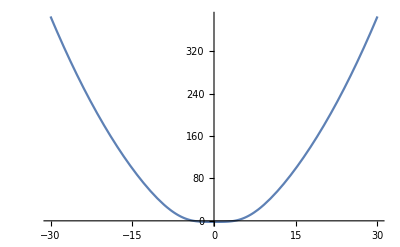

o4=pow(r,-2.);
o5=x*x;
o6=o4*o5;
o3=ma*ma;
o10=mb*mb;
o14=r*r;
o15=o14*o3;
o16=o15+o5;
o18=o10*o3;
o19=pow(x,4.);
o20=-2.*o19;
o21=o18+o20;
init0=(-3.*G*o21*r)/o16+2.*G*o21*o5*r*pow(o16,-2.)-1./sqrt(o10+o6)-1./sqrt(o3+o6);

o4=ma*ma;
o5=r*r;
o6=o4*o5;
o7=x*x;
o8=o6+o7;
o14=pow(r,-2.);
o15=o14*o7;
o11=pow(x,3.);
o19=mb*mb;
o9=pow(o8,-2.);
o24=o19*o4;
o25=pow(x,4.);
o26=-2.*o25;
o27=o24+o26;
init0prime=(24.*G*o11*r)/o8+10.*G*o27*o9*r*x+o14*x*pow(o15+o19,-1.5)+o14*x*pow(o15+o4,-1.5)\
-8.*G*o11*o27*r*pow(o8,-3.)-16.*G*o9*r*pow(x,5.);

o4=ma*ma;
o5=r*r;
o6=o4*o5;
o7=x*x;
o8=o6+o7;
o17=pow(r,-2.);
o18=o17*o7;
o19=o18+o4;
o16=pow(r,-4.);
o24=mb*mb;
o25=o18+o24;
o11=pow(x,4.);
o9=pow(o8,-3.);
o31=o24*o4;
o32=-2.*o11;
o33=o31+o32;
o12=pow(o8,-2.);
init0prime2=-208.*G*o11*o12*r+10.*G*o12*o33*r+(72.*G*o7*r)/o8-64.*G*o33*o7*o9*r-3.*o16*o7*p\
ow(o19,-2.5)+o17*pow(o19,-1.5)-3.*o16*o7*pow(o25,-2.5)+o17*pow(o25,-1.5)+48.*G*o11*o33*r*p\
ow(o8,-4.)+128.*G*o9*r*pow(x,6.);

init0.txt

initprime.txt

initprime2.txt

```mathematica
init0=(init[x] r^3)/x^2/.pθ->x//Simplify
Plot[init0/.{r->userr,ma->userm1,mb->userm2,G->userG},{x,-30,30}]
init0prime=D[init0,x];
init0prime2=D[init0prime,x];
initc=CAssign[init0,init0,"OptimizationSymbol"->o]
initcprime=CAssign[init0prime,init0prime,"OptimizationSymbol"->o]
initcprime2=CAssign[init0prime2,init0prime2,"OptimizationSymbol"->o]
Export["init0.txt",initc]
Export["initprime.txt",initcprime]
Export["initprime2.txt",initcprime2]
```

### Schwarzschild Solution

Many papers posit that using the Schwarzschild solution to solve for the angular momentum in a conserved system works for a Post-Minkowski approximation.

```mathematica
rs=(2G M)/c^2
Lz=√((μ^2 c^2 rs r^2)/(2r-3rs))//Simplify
Lz/.{c->userC,G->userG,ma->userm1,mb->userm2,r->userr}//N
%/newtonianZero[[1,1]]//N
```

(2 G (ma+mb))/c^2

√(-(c^2 G ma^2 mb^2 r^2)/((ma+mb) (3 G (ma+mb)-c^2 r)))

0.317291

1.00602

### Second Antonelli et al., 2019 solution

This is another possible solution that comes from Antonelli et al., that will likely be more complicated. This will only evaluate correctly if this notebook is set to be only two bodies.

```mathematica
γ0=(PM1^2-ma^2-mb^2)/(2ma mb);Γ=PM1/M;p0sq=μ^2(γ0^2-1)/Γ^2;f1=2 μ^2 M (2 γ0^2-1)/Γ;
p0sq+G/R[1,2] f1/.{qax->500,qbx->-500,qay->0,qby->0,pax->0,pbx->0,ma->userm1,mb->userm2,G->userG,pby->-pay}
Solve[%==pay^2,pay,Reals]//N
```

(-1+1/4 (-2+(2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π))^2)^2)/((2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π))^2)+(-1+1/2 (-2+(2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π))^2)^2)/(8000 (2 √(1+pay^2)-(7 pay^2)/(32000 π)-((1+pay^2) (1+(2 pay^2)/(1+pay^2)))/(16000 π)-(2 pay^4-(2 pay^6)/(1+pay^2)+pay^4/(√(1+pay^2)))/(32000 √(1+pay^2) (1+1/(√(1+pay^2)))^2 π)) π)

{{pay→-0.0169995},{pay→0.0169995},{pay→-745.03},{pay→745.03},{pay→-14361.6},{pay→14361.6}}